```mathematica
-------------with radial modes------------
```

```mathematica
--------without dispertion-----------
```

```mathematica
glk=Sqrt[1/(2π Factorial[Abs[l]+k]Factorial[k])]((σ w/(Sqrt[2] c))^(Abs[l]+2k))Exp[-(σ w/(Sqrt[2]c))^2];
glk1=glk/.{l->l1,k->k1};
mlkl1k1=(-I^(l-l1+1) n r0 c If[l>0,1,(-1)^(l)] If[l1>0,1,(-1)^(l1)]/(2γ T0 wb ws))/.{n->1,r0->1,c->1,γ->350,T0->1,wb->0.17,ws->0.004};
Z1=(c(Rs/(1+I Q (wR/w-w/wR)))/w)/.{c->1,Rs->5,wR->0.5,Q->5};
```

```mathematica
Mt=Table[Sum[mlkl1k1 Z1 (glk/.{w->w,σ->.5,c->1}) (glk1/.{w->w,σ->.5,c->1}),{w,-4.4,4.4,.024}],{k,0,2},{k1,0,2},{l,-2,2},{l1,-2,2}];
```

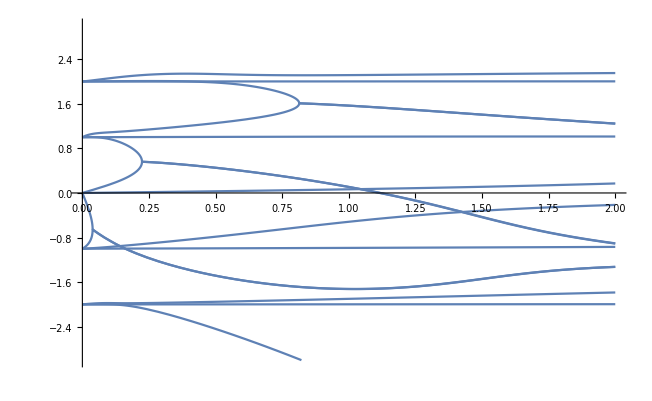

```mathematica
M=cur ArrayFlatten[Table[Mt[[i,j]],{i,1,3},{j,1,3}]]/(10^0)+DiagonalMatrix[Flatten[Table[i,{j,0,2},{i,-2,2}]]];
Plot[Sort[Re[Eigenvalues[M]]],{cur,0,2},PlotRange->{-3,3}]
```

```mathematica
---------+dispertion------------
```

```mathematica
Simplify[FunctionExpand[Pochhammer[-1/2,k]Gamma[l+3/2]HypergeometricPFQ[{3/2,3/2+l},{3/2-k,2+l},-b^2/4]]]
```

-(Gamma[-1/2+k] Gamma[3/2+l] HypergeometricPFQ[{3/2,3/2+l},{3/2-k,2+l},-b^2/4])/(2 √π)

```mathematica
glk=((σ (w)/(Sqrt[2] c))^(Abs[l]+2k))Exp[-(σ (w)/(Sqrt[2]c))^2];
glkp=((σ w/(Sqrt[2] c))^(Abs[l]+1))Pochhammer[-1/2,k]Gamma[Abs[l]+3/2]HypergeometricPFQ[{3/2,3/2+Abs[l]},{3/2-k,2+Abs[l]},-(σ w/(Sqrt[2] c))^2];
glkm=((σ w/(Sqrt[2] c))^(Abs[Abs[l]-1]))Pochhammer[Abs[l/2]-Abs[(Abs[l]-1)/2],k]Gamma[Abs[l/2]+1+Abs[(Abs[l]-1)/2]]HypergeometricPFQ[{Abs[l/2]+1+Abs[(Abs[l]-1)/2],-Abs[l/2]+1+Abs[(Abs[l]-1)/2]},{-Abs[l/2]+1+Abs[(Abs[l]-1)/2]-k,Abs[l-1]+1},-(σ w/(Sqrt[2] c))^2];
glko=Simplify[If[l>0,1,(-1)^(l)]glk+disp/dip(If[(l+1)>0,1,(-1)^(l+1)]glkp-If[(l-1)>0,1,(-1)^(l-1)]glkm)/(2I)];
glko1=Simplify[If[l1>0,1,(-1)^(l1)](glk/.{l->l1,k->k1})+disp/dip(If[(l1+1)>0,1,(-1)^(l1+1)](glkp/.{l->l1,k->k1})-If[(l1-1)>0,1,(-1)^(l1-1)](glkm/.{l->l1,k->k1}))/(2I)];
mlkl1k1=(-I^(l-l1+1) n r0 c Sqrt[1/(2π Factorial[Abs[l]+k]Factorial[k])]/(2γ T0 wb ws))/.{n->1,r0->1,c->1,γ->350,T0->1,wb->0.17,ws->0.004};
Z1=(c(Rs/(1+I Q (wR/w-w/wR)))/w)/.{c->1,Rs->5,wR->.5,Q->5};
```

```mathematica
Mt={1,2,3,4,5};
Mt[[1]]=Table[.11Sum[mlkl1k1 Z1 (glko/.{σ->.5,c->1,dip->1,disp->0}) (glko1/.{σ->.5,c->1,dip->1,disp->0}),{w,-5,5,.031}],{k,0,0},{k1,0,0},{l,-2,2},{l1,-2,2}];
```

```mathematica
Mt[[2]]=Table[.11Sum[mlkl1k1 Z1 (glko/.{σ->.5,c->1,dip->1,disp->0.33}) (glko1/.{σ->.5,c->1,dip->1,disp->0.33}),{w,-5,5,.031}],{k,0,0},{k1,0,0},{l,-2,2},{l1,-2,2}];
```

```mathematica
Mt[[3]]=Table[.11Sum[mlkl1k1 Z1 (glko/.{σ->.5,c->1,dip->1,disp->0.66}) (glko1/.{σ->.5,c->1,dip->1,disp->0.66}),{w,-5,5,.031}],{k,0,0},{k1,0,0},{l,-2,2},{l1,-2,2}];
```

```mathematica
Mt[[4]]=Table[.11Sum[mlkl1k1 Z1 (glko/.{σ->.5,c->1,dip->1,disp->1}) (glko1/.{σ->.5,c->1,dip->1,disp->1}),{w,-5,5,.031}],{k,0,0},{k1,0,0},{l,-2,2},{l1,-2,2}];
```

```mathematica
Mt[[5]]=Table[.11Sum[mlkl1k1 Z1 (glko/.{σ->.5,c->1,dip->1,disp->1.5}) (glko1/.{σ->.5,c->1,dip->1,disp->1.5}),{w,-5,5,.031}],{k,0,0},{k1,0,0},{l,-2,2},{l1,-2,2}];
```

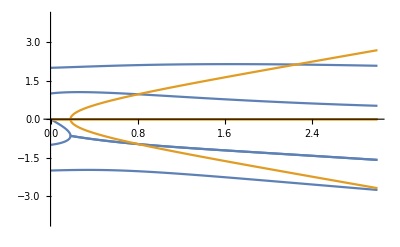
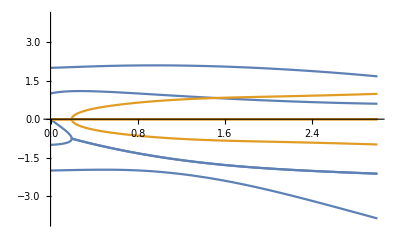
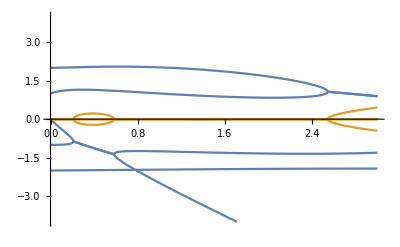
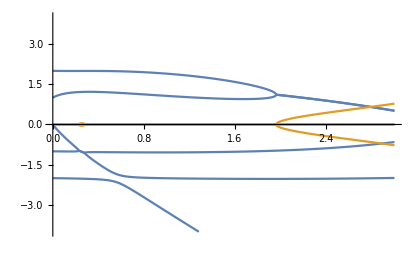
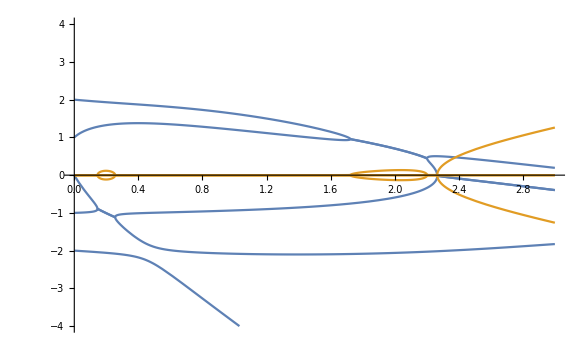

```mathematica
M=Table[cur ArrayFlatten[Table[Mt[[k]][[i,j]],{i,1,1},{j,1,1}]]/(10^0)+DiagonalMatrix[Flatten[Table[i,{j,0,0},{i,-2,2}]]],{k,1,5}];
Table[Plot[{Sort[Re[Eigenvalues[M[[k]]]]],Sort[Im[Eigenvalues[M[[k]]]]]},{cur,0,3},PlotRange->{-4,4}],{k,1,5}]
```

```mathematica
Table[HypergeometricPFQ[{1/2,1/2+Abs[l]},{1/2-k,0.01+Abs[l]},-(σ w/(Sqrt[2] c))^2]/.{σ->.5,c->1,w->1,l->0},{k,0,2}]
```

{-4.69887,5.65254,3.52527}

```mathematica
Table[HypergeometricPFQ[{3/2,3/2+Abs[l]},{3/2-k,2+Abs[l]},-(σ w/(Sqrt[2] c))^2]/.{σ->.5,c->1,w->1,l->0},{k,0,2}]
```

{0.91096,0.741962,1.21393}

```mathematica
glk=BesselJ[l,w σ/c];
glk1=glk/.{l->l1,k->k1};
mlkl1k1=(-I^(l-l1+1) n r0 c If[l>0,1,(-1)^(l)] If[l1>0,1,(-1)^(l1)]/(2γ T0 wb ws))/.{n->1,r0->1,c->1,γ->350,T0->1,wb->0.17,ws->0.004};
Z1=(c(Rs/(1+I Q (wR/w-w/wR)))/w)/.{c->1,Rs->5,wR->0.5,Q->5};
```

```mathematica
Mt=Table[Sum[mlkl1k1 Z1 (glk/.{w->w,σ->.5,c->1}) (glk1/.{w->w,σ->.5,c->1}),{w,-4.4,4.4,.014}],{k,0,0},{k1,0,0},{l,-3,3},{l1,-3,3}];
```

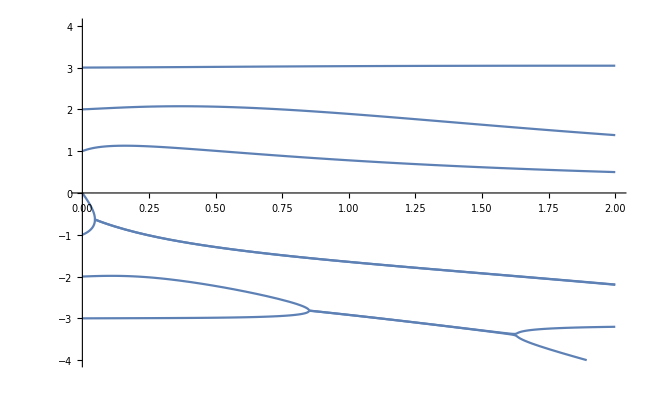

```mathematica
M=cur ArrayFlatten[Table[Mt[[i,j]],{i,1,1},{j,1,1}]]/(10^1)+DiagonalMatrix[Flatten[Table[i,{j,0,0},{i,-3,3}]]];
Plot[Sort[Re[Eigenvalues[M]]],{cur,0,2},PlotRange->{-4,4}]
```

```mathematica
glk=Sqrt[1/(2π Factorial[Abs[l]+k]Factorial[k])]((σ w/(Sqrt[2] c))^(Abs[l]+2k))Exp[-(σ w/(Sqrt[2]c))^2];
glk1=glk/.{l->l1,k->k1};
mlkl1k1=(-I^(l-l1+1) n r0 c If[l>0,1,(-1)^(l)] If[l1>0,1,(-1)^(l1)]/(2γ T0 wb ws))/.{n->1,r0->1,c->1,γ->350,T0->1,wb->0.17,ws->0.004};
Z1=(c(Rs/(1+I Q (wR/w-w/wR)))/w)/.{c->1,Rs->5,wR->0.5,Q->5};
```

```mathematica
Mt=Table[Sum[mlkl1k1 Z1 (glk/.{w->w,σ->.5,c->1}) (glk1/.{w->w,σ->.5,c->1}),{w,-4.4,4.4,.024}],{k,0,0},{k1,0,0},{l,-3,3},{l1,-3,3}];
```

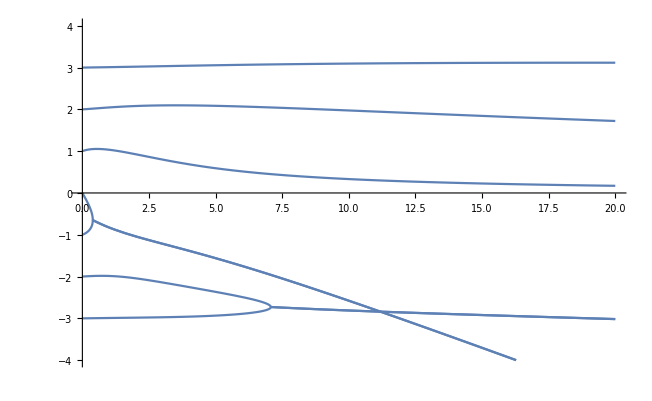

```mathematica
M=cur ArrayFlatten[Table[Mt[[i,j]],{i,1,1},{j,1,1}]]/(10^1)+DiagonalMatrix[Flatten[Table[i,{j,0,0},{i,-3,3}]]];
Plot[Sort[Re[Eigenvalues[M]]],{cur,0,20},PlotRange->{-4,4}]
```